## Incoherent transfer in Λ-system

```mathematica
ρ=Table[Subscript[a, i ,j],{i,1,3},{j,1,3}];
```

```mathematica
L1 = DiagonalMatrix[{1, -1, 0}] * Sqrt[Γ/2];
L2 = DiagonalMatrix[{1, 1, -2}] / Sqrt[3]* Sqrt[Γ/2];
Ls = {L1, L2};
incoherent = Sum[Ls[[i]].ρ.ConjugateTranspose[Ls[[i]]]-1/2 * (ρ.ConjugateTranspose[Ls[[i]]].Ls[[i]]+ConjugateTranspose[Ls[[i]]].Ls[[i]].ρ),{i, 1, Length[Ls]}];
incoherent = FullSimplify[incoherent, Assumptions->{Γ>0}];
incoherent // MatrixForm
```

(0 | -Γ a_(1,2) | -Γ a_(1,3)
-Γ a_(2,1) | 0 | -Γ a_(2,3)
-Γ a_(3,1) | -Γ a_(3,2) | 0)

```mathematica
L1 = DiagonalMatrix[{1, 0, 0}] * Sqrt[Γ];
L2 = DiagonalMatrix[{0, 1, 0}] * Sqrt[Γ];
L3 = DiagonalMatrix[{0, 0, 1}] * Sqrt[Γ];
Ls = {L1, L2, L3};
incoherent = Sum[Ls[[i]].ρ.ConjugateTranspose[Ls[[i]]]-1/2 * (ρ.ConjugateTranspose[Ls[[i]]].Ls[[i]]+ConjugateTranspose[Ls[[i]]].Ls[[i]].ρ),{i, 1, Length[Ls]}];
incoherent = FullSimplify[incoherent, Assumptions->{Γ>0}];
incoherent // MatrixForm
```

(0 | -Γ a_(1,2) | -Γ a_(1,3)
-Γ a_(2,1) | 0 | -Γ a_(2,3)
-Γ a_(3,1) | -Γ a_(3,2) | 0)

## STA in three level system

```mathematica
eqs = {D[χ[t],t] ==Tan[η[t]]*(Ω12*Sin[χ[t]]+Ω23*Cos[χ[t]]),D[η[t],t]== Ω12*Cos[χ[t]]-Ω23*Sin[χ[t]]};
FullSimplify[Solve[eqs, {Ω12, Ω23}]]
```

{{Ω12→Cos[χ[t]] η'[t]+Cot[η[t]] Sin[χ[t]] χ'[t],Ω23→-Sin[χ[t]] η'[t]+Cos[χ[t]] Cot[η[t]] χ'[t]}}

### Gutman trajectory

```mathematica
f = b*t/T + c*Sin[2*Pi*t/T]+d*Sin[4*Pi*t/T];
sol = Solve[{(f/.t->T)==Pi/2, (D[f,t]/.t->0)==0, (D[f,t]/.t->T)==0, (D[f,{t,2}]/.t->0)==0, (D[f,{t,2}]/.t->T)==0}][[1]];
f/.sol
```

(π t)/(2 T)+c Sin[(2 π t)/T]+(-1/8-c/2) Sin[(4 π t)/T]

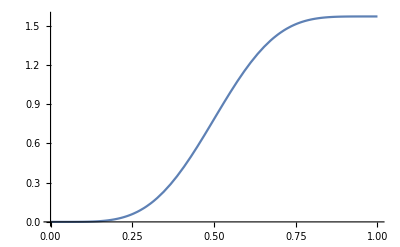

```mathematica
Plot[f/.sol/.{T->1, c->-1/3},{t,0,1}]
```

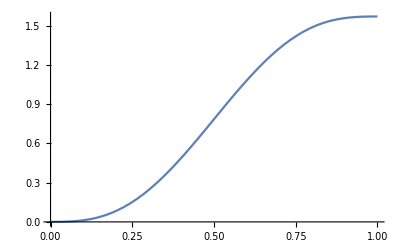

```mathematica
gutman= h*t/T -h/(2 * Pi)*(27/28*Sin[2*Pi*t/T]+1/84*Sin[4*Pi*t/T]);
Plot[gutman/.{T->1, h->Pi/2},{t,0,1}]
```